```mathematica
coefficients = Import["/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/coefficients.csv", "Dataset", "HeaderLines"-> 1];
```

```mathematica
timeframe = Normal@coefficients[All,"timeframe"];
falseVacuumCoefficient = Normal@Values@coefficients[All,{"timeframe","false_vacuum_coefficient"}];
effectivePotentialCoefficient = Normal@Values@coefficients[All,{"timeframe", "effective_potential_coefficient"}];
```

```mathematica
interpolateFalseVacuumCoefficient = Interpolation[falseVacuumCoefficient];
interpolateEffectivePotentialCoefficient = Interpolation[effectivePotentialCoefficient];
```

```mathematica
tMin = timeframe[[1]];
tMax = timeframe[[-1]];
```

```mathematica
solution = NDSolve[{-T''[t] - (3 * Cot[t] + 2 * interpolateFalseVacuumCoefficient[t])* T'[t] + interpolateEffectivePotentialCoefficient[t] * T[t] == 0, T[tMin] == 1, T'[tMin]==0}, T, {t, 0.02, 2.8}, MaxSteps->100000]⟦1,1,2⟧;
```

```mathematica
precision = Table[-solution''[t] - (3 * Cot[t] + 2 * interpolateFalseVacuumCoefficient[t])* solution'[t]+ interpolateEffectivePotentialCoefficient[t] * solution[t], {t, 0.8, 1.8, 0.0001}];
```

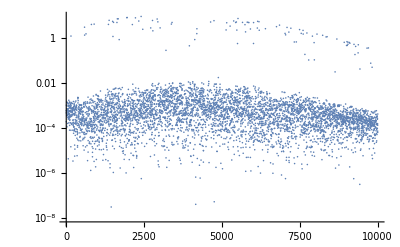

```mathematica
ListLogPlot[precision, PlotRange->All]
```

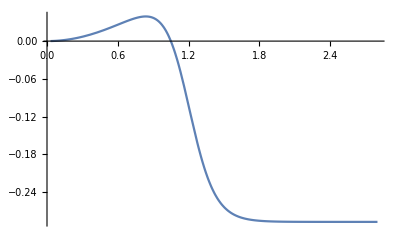

```mathematica
Plot[Log[solution[t]], {t, 0.03, 2.8}]
```

```mathematica
output = Table[solution[t], {t, timeframe}];
```

InterpolatingFunction::dmval: Input value {0.0107818} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.011096} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0114101} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
output[[1]]
```

0.749424

```mathematica
tMin
```

0.0107818

```mathematica
solution[tMin]
```

InterpolatingFunction::dmval: Input value {0.0107818} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.749424

```mathematica
Export["/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/T_solution_mathematica.csv", output, "CSV"]
```

/home/stephan/Documents/Uni/Physik/Master/Bubbles/differential_equation/solutions/T_solution_mathematica.csv

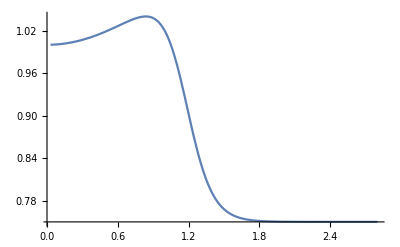

```mathematica
Plot[solution[t], {t, 0.03, 2.8}]
```

```mathematica
expansion = AsymptoticDSolveValue[{-T''[t] - (3 * Cot[t] + 2 * interpolateFalseVacuumCoefficient[t])* T'[t] + interpolateEffectivePotentialCoefficient[t] * T[t] == 0, T[0] == 1, T'[0]==0}, T[t], {t, 1, 4}];
```

```mathematica
expansion
```

AsymptoticDSolveValue[{T[t] InterpolatingFunction[…][t]-(3 Cot[t]+2 InterpolatingFunction[…][t]) T'[t]-T''[t]==0,T[0]==1,T'[0]==0},T[t],{t,1,4}]

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]

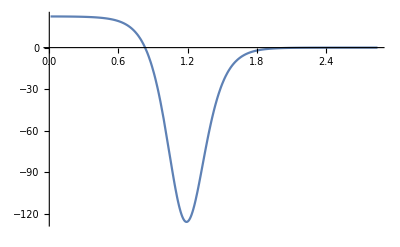

```mathematica
Plot[%25[x],{x,0.010781803202525548,2.8493139189324763}]
```